## Package

```mathematica
IDSetLinkPath["C:\Programmation\home\WORKSPACE\IDSolve\IDSolve.exe"];
```

## Simple ODE

```mathematica
λ=-1;
IDSolve[{y'[t]==λ y[t],y[0]==1},{y},{t,0,1}]
(y/.First[NDSolve[{y'[t]==λ  y[t],y[0]==1},{y},{t,0,1}]])[1.]
Exp[-1]//N
```

{Interval[{0.367879,0.367879}]}

0.367879

0.367879

## Falling ball

```mathematica
eqns[x_, y_, sx_, sy_, g_]={x1'[t] == v1[t] , x0'[t]  == v0[t] , v0'[t]  ==0, v1'[t] == -g ,
x0[0] == x, x1[0] == y,v0[0] == sx,v1[0] == sy};
tend = 1;
```

```mathematica
eqns[0, 5, 2, 0,Interval[{9.,10.}]]
```

{x1'[t]==v1[t],x0'[t]==v0[t],v0'[t]==0,v1'[t]==Interval[{-10.,-9.}],x0[0]==0,x1[0]==5,v0[0]==2,v1[0]==0}

{Interval[{1.9,2.1}],Interval[{-0.005,0.195}],Interval[{2.,2.}],Interval[{-9.81,-9.81}]}

{2.,0.095,2.,-9.81}

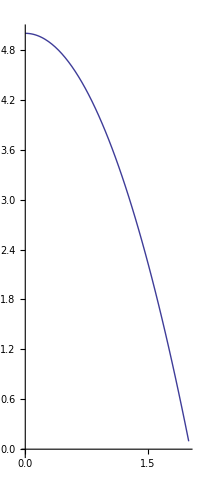

```mathematica
IDSolve[eqns[Interval[{-0.1,0.1}], Interval[{4.9,5.1}], 2, 0,9.81],{ x0, x1, v0, v1},{t,0, tend}]
nd = NDSolve[eqns[0, 5, 2, 0, 9.81],{ x0, x1,v0, v1},{t,0, tend}];
{posx,posy, spdx, spdy}={x0, x1,v0, v1}/.First[nd];
{posx[tend], posy[tend], spdx[tend], spdy[tend]}
ParametricPlot[{posx[t],posy[t]},{t,0,tend}]
```

## Lorenz

```mathematica
σ=10.;
β=N[8/3];
ρ=28.;
```

```mathematica
{sx,sy,sz}={x,y,z}/.First[NDSolve[{x'[t]==σ (y[t]-x[t]),y'[t]==x[t](ρ-z[t])-y[t],z'[t]==x[t]y[t]-β z[t],x[0]==1,y[0]==1,z[0]==1},{x,y,z},{t,0,50}]]
```

{InterpolatingFunction[{{0.,50.}},<>],InterpolatingFunction[{{0.,50.}},<>],InterpolatingFunction[{{0.,50.}},<>]}

```mathematica
ParametricPlot3D[{sx[t],sy[t],sz[t]},{t,0,50}]
```

-Graphics3D-

```mathematica
IDSolve[{x'[t]==σ (y[t]-x[t]),y'[t]==x[t](ρ-z[t])-y[t],z'[t]==x[t]y[t]-β z[t],x[0]==1,y[0]==1,z[0]==1},{x,y,z},{t,0,32.85}]
IDSolve[{x'[t]==σ (y[t]-x[t]),y'[t]==x[t](ρ-z[t])-y[t],z'[t]==x[t]y[t]-β z[t],x[0]==1,y[0]==1,z[0]==1},{x,y,z},{t,0,32.9}]
```

{Interval[{-57.0724,79.8207}],Interval[{-253.41,242.98}],Interval[{-210.348,293.065}]}

Message::name: Message name IDSolve::reach is not of the form symbol::name or symbol::name::language.

Message[IDSolve::reach,t,Interval[{32.9,32.9}]]

```mathematica
dt=0.47;
nstep=40;
sol=NestList[IDSolve[{x'[t]==σ (y[t]-x[t]),y'[t]==x[t](ρ-z[t])-y[t],z'[t]==x[t]y[t]-β z[t],x[0]==#[[1]],y[0]==#[[2]],z[0]==#[[3]]},{x,y,z},{t,0,dt}]&,{1.,1.,1.},nstep];
```

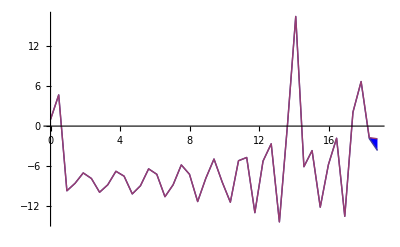

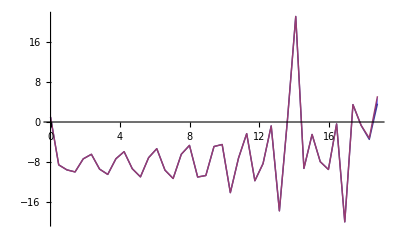

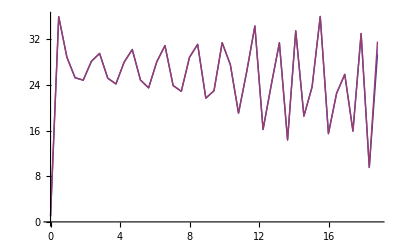

```mathematica
ListPlot[{Map[Min[#[[1]]]&,sol],Map[Max[#[[1]]]&,sol]},Joined->True,DataRange->{0,dt nstep},Filling->{1->{{2},Blue}}]
ListPlot[{Map[Min[#[[2]]]&,sol],Map[Max[#[[2]]]&,sol]},Joined->True,DataRange->{0,dt nstep},Filling->{1->{{2},Blue}}]
ListPlot[{Map[Min[#[[3]]]&,sol],Map[Max[#[[3]]]&,sol]},Joined->True,DataRange->{0,dt nstep},Filling->{1->{{2},Blue}}]
```